```mathematica
FitForNi[x_]:=Module[{dataWithErrors,data,errors,a,b,niMin,niMax,dNi,errNi,lf,bestNi,Nc},
dataWithErrors=Table[{m[[1]],Around[m[[3,1]],m[[3,2]]]},{m,x}];
niMin=Min[x[[;;,1]]];
niMax=Max[x[[;;,1]]];
Nc=Mean[x[[;;,2]]];
data=Table[{m[[1]],m[[3,1]]},{m,x}];
errors=Table[m[[3,2]],{m,x}];
lf=LinearModelFit[data,ni,ni,Weights->1/errors^2];
Print["R^2=",lf["RSquared"]];
Print[Show[ListPlot[dataWithErrors],Plot[{lf[ni],50},{ni,niMin,niMax}]]];
{a,b}=lf["BestFitParameters"];
bestNi = (50-a)/b;
dNi={-1/b,(a-50)/b^2};
errNi=Sqrt[dNi.lf["CovarianceMatrix"].dNi];
{Nc,Around[bestNi,errNi]}
]
```

```mathematica
FitForNc[x_]:=Module[{dataWithErrors,data,errors,a,b,ncMin,ncMax,dNc,errNc,lf,bestNc,Ni},
dataWithErrors=Table[{m[[2]],Around[m[[3,1]],m[[3,2]]]},{m,x}];
ncMin=Min[x[[;;,2]]];
ncMax=Max[x[[;;,2]]];
Ni=Mean[x[[;;,1]]];
data=Table[{m[[2]],m[[3,1]]},{m,x}];
errors=Table[m[[3,2]],{m,x}];
lf=LinearModelFit[data,nc,nc,Weights->1/errors^2];
Print["R^2=",lf["RSquared"]];
Print[Show[ListPlot[dataWithErrors],Plot[{lf[nc],50},{nc,ncMin,ncMax}]]];
{a,b}=lf["BestFitParameters"];
bestNc = (50-a)/b;
dNc={-1/b,(a-50)/b^2};
errNc=Sqrt[dNc.lf["CovarianceMatrix"].dNc];
{Around[bestNc,errNc],Ni}
]
```

R^2=0.993899

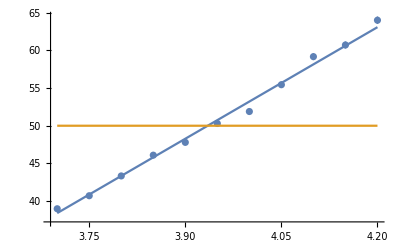

{3.9350.004,100.}

```mathematica
paschNc=FitForNc[{{100.000,3.700,{38.97,0.31}},{100.000,3.750,{40.70,0.32}},{100.000,3.800,{43.33,0.34}},{100.000,3.850,{46.09,0.36}},{100.000,3.900,{47.79,0.37}},{100.000,3.950,{50.30,0.39}},{100.000,4.000,{51.89,0.41}},{100.000,4.050,{55.45,0.43}},{100.000,4.100,{59.18,0.46}},{100.000,4.150,{60.73,0.47}},{100.000,4.200,{64.02,0.50}}}]
```

```mathematica
runs={
{
{11.800,7.000,{42.96,0.34}},{11.980,7.000,{43.58,0.36}},{12.160,7.000,{45.17,0.37}},{12.340,7.000,{47.86,0.39}},{12.520,7.000,{50.20,0.42}},{12.700,7.000,{51.40,0.43}},{12.880,7.000,{51.99,0.44}},{13.060,7.000,{54.08,0.47}},{13.240,7.000,{55.89,0.49}},{13.420,7.000,{57.25,0.50}},{13.600,7.000,{60.47,0.54}}
},
{
{10.000,10.000,{39.23,0.43}},{10.100,10.000,{41.28,0.45}},{10.200,10.000,{42.57,0.48}},{10.300,10.000,{43.69,0.51}},{10.400,10.000,{46.01,0.53}},{10.500,10.000,{46.70,0.54}},{10.600,10.000,{49.65,0.57}},{10.700,10.000,{50.84,0.59}},{10.800,10.000,{51.47,0.61}},{10.900,10.000,{53.39,0.64}},{11.000,10.000,{55.94,0.65}}
},
{
{11.000,20.000,{44.49,0.53}},{11.040,20.000,{45.88,0.56}},{11.080,20.000,{46.62,0.57}},{11.120,20.000,{47.97,0.58}},{11.160,20.000,{48.62,0.58}},{11.200,20.000,{49.50,0.62}},{11.240,20.000,{50.72,0.62}},{11.280,20.000,{53.30,0.63}},{11.320,20.000,{52.58,0.62}},{11.360,20.000,{54.66,0.64}},{11.400,20.000,{55.86,0.63}}
},
{
{14.400,40.000,{37.82,0.67}},{14.500,40.000,{40.08,0.71}},{14.600,40.000,{41.45,0.73}},{14.700,40.000,{45.51,0.81}},{14.800,40.000,{47.85,0.83}},{14.900,40.000,{51.37,0.86}},{15.000,40.000,{54.43,0.95}},{15.100,40.000,{59.88,1.02}},{15.200,40.000,{62.11,1.08}},{15.300,40.000,{64.25,1.12}},{15.400,40.000,{69.81,1.20}}
},
{
{22.200,80.000,{43.92,0.48}},{22.260,80.000,{45.37,0.51}},{22.320,80.000,{47.02,0.52}},{22.380,80.000,{48.52,0.55}},{22.440,80.000,{50.56,0.55}},{22.500,80.000,{52.56,0.57}},{22.560,80.000,{53.09,0.59}},{22.620,80.000,{55.48,0.60}},{22.680,80.000,{57.67,0.62}},{22.740,80.000,{58.54,0.65}},{22.800,80.000,{60.12,0.66}}
},
{{36.200,160.000,{41.55,0.48}},{36.280,160.000,{42.74,0.50}},{36.360,160.000,{44.00,0.52}},{36.440,160.000,{45.82,0.53}},{36.520,160.000,{49.03,0.56}},{36.600,160.000,{50.18,0.58}},{36.680,160.000,{50.56,0.57}},{36.760,160.000,{52.77,0.61}},{36.840,160.000,{55.48,0.63}},{36.920,160.000,{56.55,0.66}},{37.000,160.000,{59.64,0.70}}
},
{
{62.000,320.000,{41.69,0.86}},{62.100,320.000,{43.87,0.88}},{62.200,320.000,{44.95,0.89}},{62.300,320.000,{45.87,0.92}},{62.400,320.000,{47.92,0.99}},{62.500,320.000,{51.07,1.01}},{62.600,320.000,{50.99,1.02}},{62.700,320.000,{50.66,1.01}},{62.800,320.000,{55.08,1.11}},{62.900,320.000,{54.98,1.06}},{63.000,320.000,{56.64,1.13}}
},
{
{109.000,640.000,{41.39,0.39}},{109.160,640.000,{42.90,0.41}},{109.320,640.000,{44.31,0.43}},{109.480,640.000,{45.46,0.43}},{109.640,640.000,{46.40,0.44}},{109.800,640.000,{49.64,0.47}},{109.960,640.000,{50.23,0.47}},{110.120,640.000,{53.32,0.50}},{110.280,640.000,{53.87,0.51}},{110.440,640.000,{56.74,0.54}},{110.600,640.000,{59.13,0.55}}
}
};
```

R^2=0.987443

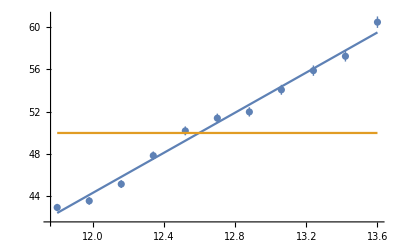

R^2=0.992655

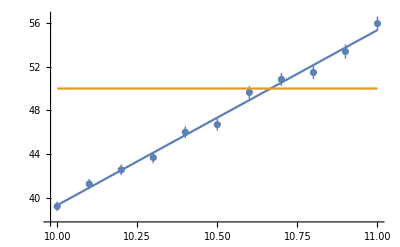

R^2=0.983732

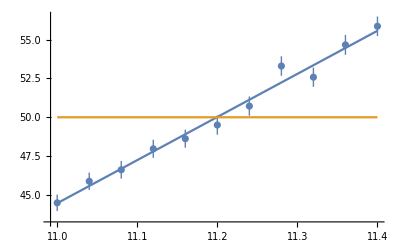

R^2=0.987671

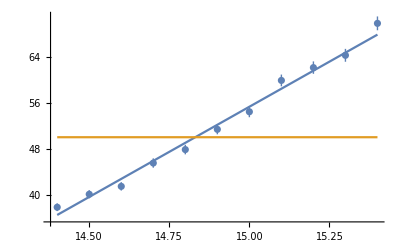

R^2=0.99624

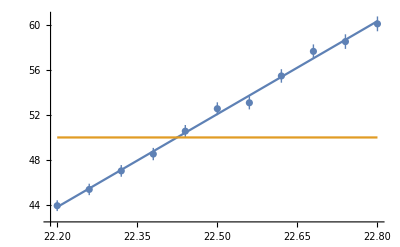

R^2=0.987202

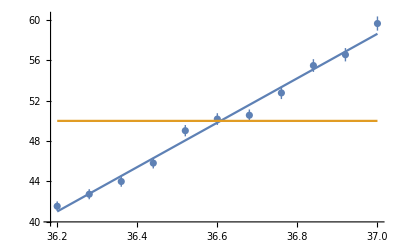

R^2=0.970103

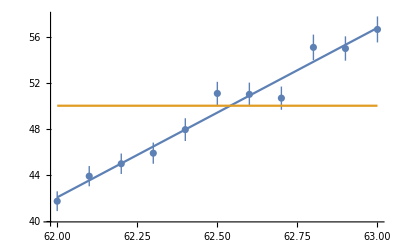

R^2=0.9838

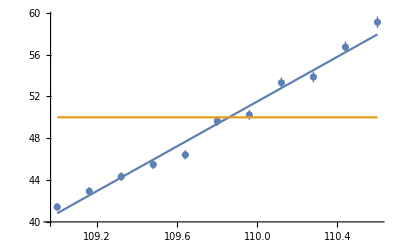

{{7.,12.5970.021},{10.,10.6660.011},{20.,11.1990.006},{40.,14.8310.011},{80.,22.4250.004},{160.,36.6080.010},{320.,62.5410.019},{640.,109.8580.022}}

```mathematica
pasch=Table[FitForNi[x],{x,runs}]
```

```mathematica
Prepend[pasch,paschNc]
```

{{3.9350.004,100.},{7.,12.5970.021},{10.,10.6660.011},{20.,11.1990.006},{40.,14.8310.011},{80.,22.4250.004},{160.,36.6080.010},{320.,62.5410.019},{640.,109.8580.022}}

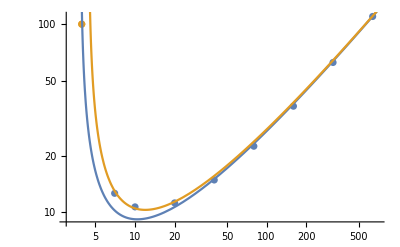

```mathematica
Show[ListLogLogPlot[{pasch,{paschNc}},PlotRange->{{3,700},All}],LogLogPlot[{(0.88pd)/Log[pd/3.83],(0.86pd)/Log[pd/4.4]},{pd,3.8,700}]]
```

```mathematica
Log[45]/.8
```

4.75833

```mathematica
Exp[3.8]
```

44.7012

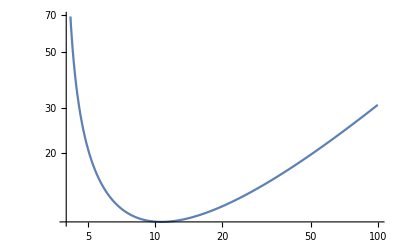

```mathematica
LogLogPlot[Nc/(Log[Nc]-Log[Log[51]]),{Nc,4,100}]
```

```mathematica
x={#[[1]],Around[#[[2,1]],#[[2,2]]]}&/@{{10.000,{47.61,0.56}},{10.800,{48.54,0.53}},{11.600,{49.91,0.53}},{12.400,{51.44,0.52}},{13.200,{50.60,0.54}},{14.000,{49.46,0.53}},{14.800,{48.75,0.50}},{15.600,{46.97,0.53}},{16.400,{44.62,0.47}},{17.200,{43.29,0.49}},{18.000,{40.34,0.47}}}
```

{{10.,47.60.6},{10.8,48.50.5},{11.6,49.90.5},{12.4,51.40.5},{13.2,50.60.5},{14.,49.50.5},{14.8,48.80.5},{15.6,47.00.5},{16.4,44.60.5},{17.2,43.30.5},{18.,40.30.5}}

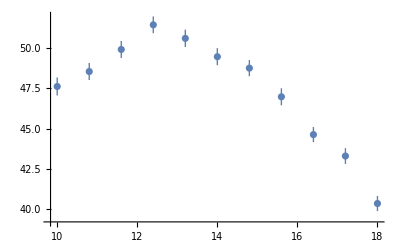

```mathematica
ListPlot[x]
```

```mathematica
12.5/3.8
```

3.28947

```mathematica
x
```

{{10.,{47.61,0.56}},{10.8,{48.54,0.53}},{11.6,{49.91,0.53}},{12.4,{51.44,0.52}},{13.2,{50.6,0.54}},{14.,{49.46,0.53}},{14.8,{48.75,0.5}},{15.6,{46.97,0.53}},{16.4,{44.62,0.47}},{17.2,{43.29,0.49}},{18.,{40.34,0.47}}}